# Discontinuous Galerkin

## Weak Formulation (Modal DG)

Manuel Diaz, 
2013.07.19

## Legendre Polynomials

```mathematica
legendreP =Table[LegendreP[i,z],{i,0,6}];
Column[legendreP] /.z->𝒳// TraditionalForm
```

1
𝒳
1/2 (3 𝒳^2-1)
1/2 (5 𝒳^3-3 𝒳)
1/8 (35 𝒳^4-30 𝒳^2+3)
1/8 (63 𝒳^5-70 𝒳^3+15 𝒳)
1/16 (231 𝒳^6-315 𝒳^4+105 𝒳^2-5)

## Plot Legendre Polynomials

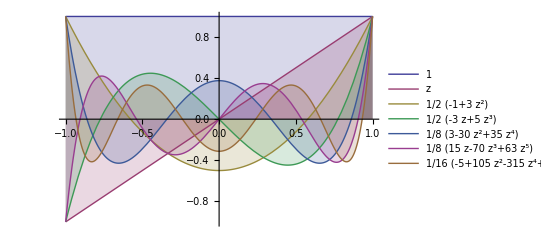

```mathematica
Plot[Evaluate[legendreP],{z,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

## Properties

#### Initialize Notation

```mathematica
Needs["Notation`"]
```

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{z,-1,1}]]
```

#### Give a name to each Legendre Polynomial

```mathematica
{Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5],Subscript[p, 6]} = legendreP;
```

#### Evaluate Orthogonality

```mathematica
Table[(<Subscript[p, i],Subscript[p, j]>),{i,0,6},{j,0,6}] //MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2/5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2/7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2/9 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2/11 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2/13)

## Reference

Jian-Xian Qiu & Chi-Wang Shu

Runge-Kutta Discontinuous Galerkin Method Using WENO Limiters
SIAM 2005.

Here we try to solve the one dimensional conservation Law,

u_t+f_x(u) ==0

with

u[x,0] = u_0[x]

## Method

Use a grid of cell defined as I_j=[x_(j+1/2),x_(j-1/2)], where x_j is the cell center.
The individual cell size is defined as Δx_j= x_(j-1/2)-x_(j+1/2) and the maximun cell size is h = sup_j Δx_j.

```mathematica
Symbolize[Subscript[Δx, j]]; Symbolize[Subscript[x, j]];Symbolize[Subscript[I, j]];
```

Using Galerkin Method the solution and the test function are given by V_j^h={p:p|_I_j∈ P^k(I_j)}, where P^K(I_j) is the space of polynomials of degree ≤ k on the cell I_j.

To fullil this last requirmente we require polynomials basis that provieds two requirements:
1. Provides good interpolation properties inside I_j.
2. Provides delta function δ_ij properties.

#### Main Approaches

1. Use Legendre Polynomials using a Local/Normalized coordiante, ξ for range [-1,1] as traditionally in FEM.
2. Build scalated Legendre Polynomials to work in I_j for the range [x_(j+1/2),x_(j-1/2)] or in the case of a uniform grid [-Δx/2,Δx/2].

## Scaled Legendre Polynomials

This polynomials will have the form:

v_0 = 1; v_1= (x-x_j)/Δx_j; v_2= ((x-x_j)/Δx_j)^2-1/12; ...

How to build this scalated orthogonal polynomials?

### Building Orthogonal Polynomials

#### Using Gram Schmidt Orthogonalization process

based on http://en.wikipedia.org/wiki/Gram-Schmidt_process, we configure:

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{z,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
```

```mathematica
Notation[<a_[x_],b_[x_]> ⟹ Integrate[a_[x_] b_[x_],{x_,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
```

```mathematica
Notation[Subscript[proj, u_][v_] ⟹ (<u_,v_>)/(<u_,u_>)u_]
```

## Testing Notation

Inner Product of functions

```mathematica
<Subscript[v, 1][z],Subscript[v, 1][z]>
```

∫_(-Δx_j/2)^(Δx_j/2) v_1[z]^2 ⅆz

Inner product of name variables

```mathematica
<a z,z>
```

(a Δx_j^3)/12

Projection method

```mathematica
(<a[z],b[z]>)/(<a[z],a[z]>)a[z] == Subscript[proj, a[z]][b[z]]
```

True

### Building Scaled Legendre Polynomials using Gram Schmidt Orthogonalization process

based on http : // mathworld.wolfram.com/Gram - SchmidtOrthonormalization.html, we configure :

```mathematica
Subscript[p, 0]=1;
Subscript[p, 1]=(z - (<z Subscript[p, 0],Subscript[p, 0]>)/(<Subscript[p, 0],Subscript[p, 0]>))Subscript[p, 0];
```

```mathematica
scaledLegendre=Table[Subscript[p, i+1]=(z - (<z Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i],Subscript[p, i]>))Subscript[p, i] -(<Subscript[p, i],Subscript[p, i]>)/(<Subscript[p, i-1],Subscript[p, i-1]>)Subscript[p, i-1] ,{i,1,5}]//Expand ;
scaledLegendre = Join[{Subscript[p, 0],Subscript[p, 1]},scaledLegendre];
```

```mathematica
scaledLegendre //Column
```

1
z
z^2-Δx_j^2/12
z^3-(3 z Δx_j^2)/20
z^4-3/14 z^2 Δx_j^2+(3 Δx_j^4)/560
z^5-5/18 z^3 Δx_j^2+(5 z Δx_j^4)/336
z^6-15/44 z^4 Δx_j^2+5/176 z^2 Δx_j^4-(5 Δx_j^6)/14784

## Substituting ‘z’ variable

```mathematica
scaledLegendre /.z-> x-Subscript[x, j]//Column
```

1
x-x_j
(x-x_j)^2-Δx_j^2/12
(x-x_j)^3-3/20 (x-x_j) Δx_j^2
(x-x_j)^4-3/14 (x-x_j)^2 Δx_j^2+(3 Δx_j^4)/560
(x-x_j)^5-5/18 (x-x_j)^3 Δx_j^2+5/336 (x-x_j) Δx_j^4
(x-x_j)^6-15/44 (x-x_j)^4 Δx_j^2+5/176 (x-x_j)^2 Δx_j^4-(5 Δx_j^6)/14784

```mathematica
scaledLegendre2 =Divide[scaledLegendre,{1,Subscript[Δx, j],Subscript[Δx, j]^2,Subscript[Δx, j]^3,Subscript[Δx, j]^4,Subscript[Δx, j]^5,Subscript[Δx, j]^6}]//Expand ;
scaledLegendre2/.z->x-Subscript[x, j]//Column
```

1
(x-x_j)/Δx_j
-1/12+(x-x_j)^2/Δx_j^2
(x-x_j)^3/Δx_j^3-(3 (x-x_j))/(20 Δx_j)
3/560+(x-x_j)^4/Δx_j^4-(3 (x-x_j)^2)/(14 Δx_j^2)
(x-x_j)^5/Δx_j^5-(5 (x-x_j)^3)/(18 Δx_j^3)+(5 (x-x_j))/(336 Δx_j)
-5/14784+(x-x_j)^6/Δx_j^6-(15 (x-x_j)^4)/(44 Δx_j^4)+(5 (x-x_j)^2)/(176 Δx_j^2)

#### Alternative procedure: (the mathematica way)

```mathematica
scaledLegendre3 = Orthogonalize[{1,z,z^2,z^3,z^4,z^5,z^6},Integrate[#1 #2,{z,-1/2,1/2}]&] //Expand;
```

```mathematica
scaledLegendre3 /.z->(x-Subscript[x, j])/Subscript[Δx, j]//Column
```

1
(2 √3 (x-x_j))/Δx_j
-(√5)/2+(6 √5 (x-x_j)^2)/Δx_j^2
(20 √7 (x-x_j)^3)/Δx_j^3-(3 √7 (x-x_j))/Δx_j
9/8+(210 (x-x_j)^4)/Δx_j^4-(45 (x-x_j)^2)/Δx_j^2
(252 √11 (x-x_j)^5)/Δx_j^5-(70 √11 (x-x_j)^3)/Δx_j^3+(15 √11 (x-x_j))/(4 Δx_j)
-(5 √13)/16+(924 √13 (x-x_j)^6)/Δx_j^6-(315 √13 (x-x_j)^4)/Δx_j^4+(105 √13 (x-x_j)^2)/(4 Δx_j^2)

Their orthogonal behavior:

Here, I need to re-define in this case my notation becuase here the integration is obver the classical range of [-1,1]

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{z,-1,1}]]
```

```mathematica
Table[(<scaledLegendre3[[i]],scaledLegendre3[[j]]>),{i,1,7},{j,1,7}] //MatrixForm
```

(2 | 0 | 3 √5 | 0 | 225/4 | 0 | (1239 √13)/8
0 | 8 | 0 | 12 √21 | 0 | 93 √33 | 0
3 √5 | 0 | 109/2 | 0 | (1827 √5)/8 | 0 | (10821 √65)/16
0 | 12 √21 | 0 | 506 | 0 | (1221 √77)/2 | 0
225/4 | 0 | (1827 √5)/8 | 0 | 170689/32 | 0 | (1065591 √13)/64
0 | 93 √33 | 0 | (1221 √77)/2 | 0 | 479209/8 | 0
(1239 √13)/8 | 0 | (10821 √65)/16 | 0 | (1065591 √13)/64 | 0 | 89512861/128)

Therefore this are normalized and scaled legrendre polynomials!

### Normalization Constants

```mathematica
coefficients = Table[(<Subscript[p, n],Subscript[p, m]>),{n,0,6},{m,0,6}];
```

```mathematica
coefficients // TableForm
```

Δx_j | 0 | 0 | 0 | 0 | 0 | 0
0 | Δx_j^3/12 | 0 | 0 | 0 | 0 | 0
0 | 0 | Δx_j^5/180 | 0 | 0 | 0 | 0
0 | 0 | 0 | Δx_j^7/2800 | 0 | 0 | 0
0 | 0 | 0 | 0 | Δx_j^9/44100 | 0 | 0
0 | 0 | 0 | 0 | 0 | Δx_j^11/698544 | 0
0 | 0 | 0 | 0 | 0 | 0 | Δx_j^13/11099088

```mathematica
coef = Diagonal[coefficients]; Table[Subscript[a, i]=coef[[i+1]],{i,0,6}]
```

{Δx_j,Δx_j^3/12,Δx_j^5/180,Δx_j^7/2800,Δx_j^9/44100,Δx_j^11/698544,Δx_j^13/11099088}

#### Derivative of the scaled polynomials

```mathematica
dscaledpolynomials = D[scaledLegendre,z];
dscaledpolynomials /.z -> (x-Subscript[x, j])/Subscript[Δx, j] //Column
```

0
1
(2 (x-x_j))/Δx_j
(3 (x-x_j)^2)/Δx_j^2-(3 Δx_j^2)/20
(4 (x-x_j)^3)/Δx_j^3-3/7 (x-x_j) Δx_j
-5/6 (x-x_j)^2+(5 (x-x_j)^4)/Δx_j^4+(5 Δx_j^4)/336
(6 (x-x_j)^5)/Δx_j^5-(15 (x-x_j)^3)/(11 Δx_j)+5/88 (x-x_j) Δx_j^3

```mathematica
Table[Subscript[dp, i]= dscaledpolynomials[[i+1]],{i,0,6}];
```

```mathematica
dcoefficients = Table[Subscript[b, n,m]= (<Subscript[p, n],Subscript[dp, m]>),{n,0,6},{m,0,6}];
```

```mathematica
dcoefficients //TableForm
```

0 | Δx_j | 0 | Δx_j^3/10 | 0 | Δx_j^5/126 | 0
0 | 0 | Δx_j^3/6 | 0 | Δx_j^5/70 | 0 | Δx_j^7/924
0 | 0 | 0 | Δx_j^5/60 | 0 | Δx_j^7/756 | 0
0 | 0 | 0 | 0 | Δx_j^7/700 | 0 | Δx_j^9/9240
0 | 0 | 0 | 0 | 0 | Δx_j^9/8820 | 0
0 | 0 | 0 | 0 | 0 | 0 | Δx_j^11/116424
0 | 0 | 0 | 0 | 0 | 0 | 0

## Numerical Solution and Degress Of Freedom

Then the numerical Solution u^h[x,t] in the space V_j^K can be written as:

u^h[x,t] = ∑_(l=0)^k a_l u_j^(l)[t]v_l^(j)[x], for x ∈ I_j

And the degrees of freedom u_j^(l)[t] are the moments defined by:

u_j^(l) = u_j^(l)[t] = 1/Δx_j^(l+1)∫_I_j u[x,t] v_l^(j)[x]ⅆx, for l = 1,...,k

## Basis Function for 1D cases:

Here we are interested in understanding the expansion of these polynomials from their continuous initial form to a piezewize form.

Recal from previous calculations we can do :

```mathematica
Subscript[p, 5]
```

-4/63 Δx_j^2 (-1/15 z Δx_j^2+z (z^2-Δx_j^2/12))+z (-9/140 Δx_j^2 (z^2-Δx_j^2/12)+z (-1/15 z Δx_j^2+z (z^2-Δx_j^2/12)))

Then we can create our table of scalled polynomials:

```mathematica
Table[Subscript[v, i]= Expand[Subscript[p, i]],{i,0,6}];(* recall that z -> (x-Subscript[x, j])/Subscript[Δx, j] *)
Table[Subscript[v, i],{i,0,6}]//MatrixForm
```

(1
z
z^2-Δx_j^2/12
z^3-(3 z Δx_j^2)/20
z^4-3/14 z^2 Δx_j^2+(3 Δx_j^4)/560
z^5-5/18 z^3 Δx_j^2+(5 z Δx_j^4)/336
z^6-15/44 z^4 Δx_j^2+5/176 z^2 Δx_j^4-(5 Δx_j^6)/14784)

Now must assume the location of the abcissas. Following our main reference we proceed to use Gauss-Lobatto-Legendre for 4 points scaled to fit in I_j, the corresponding local coordiantes of the abscissas and weight are:

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]} = {-1/2,-(√5)/10,(√5)/10,1/2}; {Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4]}={1/12,5/12,5/12,1/12};
```

As an example, here I’ll assume an interval, I_j, with left and right boundaries located at [-1/6,1/6]. 
First we proceed to create the corresponding local nodes inside the cell:

```mathematica
Symbolize[Subscript[x, r]];Symbolize[Subscript[x, l]];
```

```mathematica
Subscript[x, l] = -1/6; Subscript[x, r] =1/6; Subscript[Δx, j]=Subscript[x, r]-Subscript[x, l];Subscript[x, j] = Subscript[Δx, j]/2; {Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]} =Subscript[x, j]+{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]} Subscript[Δx, j]
```

{0,1/6-1/(6 √5),1/6+1/(6 √5),1/3}

Notice that the Global coordinates will be given by,

```mathematica
X= Subscript[x, l]+{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}
```

{-1/6,-1/(6 √5),1/(6 √5),1/6}

### Degrees of Freedom u_j^(l)

For u_j element using the continuous function u(x,t). If we define the degrees of freedom as:

u_j^(l) = u_j^(l)[t] = 1/Δx_j^(l+1)∫_I_j u[x,t] v_l^(j)[x]ⅆx, for l = 1,...,k

```mathematica
Notation[∫_Subscript[I, j] f_ⅆx_ ⟹ Integrate[f_,{x_,-Subscript[Δx, j]/2,Subscript[Δx, j]/2}]]
```

Of course, we will need to define u[x,t] in order to continue. i.e., to define u[x,0] =u_0[x].
We traditionally have two choises a continuous or a discontinuous function,

#### Case1: Riemann IC

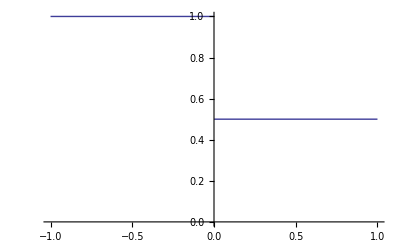

```mathematica
u[x_,t_]:= Piecewise[{{1,x<0},{0.5,x>=0}}];
Plot[u[x,t],{x,-1,1},PlotRange->{0,1}]
```

#### Case2: Sinusoidal wave function

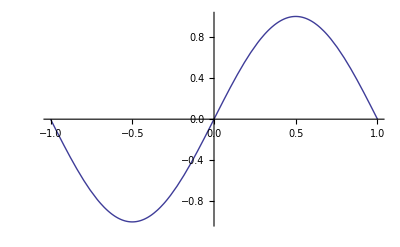

```mathematica
u[x_,t_]:= Sin[π x];
Plot[u[x,t],{x,-1,1},PlotRange->Full]
```

## Degress of Freedom, u_j^(l)(t)

Having defined a u[x,t],

```mathematica
Symbolize[Subscript[u, h]];Symbolize[u^_];
```

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} = Table[ 1/Subscript[a, l]∫_Subscript[I, j] (u[z,t] Subscript[v, l])ⅆz,{l,0,6}];
```

Evaluate Numerically

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} //N//MatrixForm 
{Subscript[u, 0],Subscript[u, 1],Subscript[u, 2],Subscript[u, 3],Subscript[u, 4],Subscript[u, 5],Subscript[u, 6]}={u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)} ;
```

(0.75
-2.25
0.
118.125
0.
-10524.9
0.)

## Numerical Solution, u_h(x,t)

Following the last example we can proceed to compute from the degress of freedom the approximate solution u_h,

```mathematica
Subscript[u, h]=N[Sum[Subscript[u, l] Subscript[v, l],{l,0,6}]/. z->Subscript[x, l]]
```

1.07813

## Alternative way to compute u_h and u_j^(l)

Building a Vandermonde Matrix: 
-> Evaluate every escaled polynomial for the computed abcisas we get:

```mathematica
V= Table[Subscript[q, i][Subscript[𝓍, n]],{n,1,4},{i,0,3}] //MatrixForm
```

(q_0[𝓍_1] | q_1[𝓍_1] | q_2[𝓍_1] | q_3[𝓍_1]
q_0[𝓍_2] | q_1[𝓍_2] | q_2[𝓍_2] | q_3[𝓍_2]
q_0[𝓍_3] | q_1[𝓍_3] | q_2[𝓍_3] | q_3[𝓍_3]
q_0[𝓍_4] | q_1[𝓍_4] | q_2[𝓍_4] | q_3[𝓍_4])

```mathematica
V= Table[Subscript[v, i]/.z->Subscript[x, n],{n,1,4},{i,0,3}];
V //MatrixForm
```

(1 | 0 | -1/108 | 0
1 | 1/6-1/(6 √5) | -1/108+(1/6-1/(6 √5))^2 | (1/6-1/(6 √5))^3+1/60 (-1/6+1/(6 √5))
1 | 1/6+1/(6 √5) | -1/108+(1/6+1/(6 √5))^2 | 1/60 (-1/6-1/(6 √5))+(1/6+1/(6 √5))^3
1 | 1/3 | 11/108 | 17/540)

if we are using equally distributed cells, we can just program the numerical version of this matrix:

```mathematica
V//N//MatrixForm
```

(1. | 0. | -0.00925926 | 0.
1. | 0.0921311 | -0.000771126 | -0.000753497
1. | 0.241202 | 0.0489193 | 0.0100128
1. | 0.333333 | 0.101852 | 0.0314815)

Thus, for the degress of freedom,

```mathematica
(Subscript[u, j]^(l))[t] = (V^-1).u[x,t]
```

and for the approximate solution,

```mathematica
Subscript[u, h][x,t]= V . (Subscript[u, j]^(l))[t]
```

See my Matlab Burger’s implementation for details...

## The Conservation Equation

For hyperbolic conservation that we are targeting,

∂_t u+∑_(i=1)^d ∂_i f[u]=0

We are basicly interested in evoling the degrees of freedom u_j^(l), following our main reference,

∂/(∂t)u_i^(l)+1/a_l(- ∫_I_j f(u^h[x,t])d/dx v_l^(j)ⅆx+f[(u_(j+1/2))^-,(u_(j+1/2))^+]v_l^(j)[x_(j+1/2)]-f[(u_(j-1/2))^-,(u_(j-1/2))^+]v_l^(j)[x_(j-1/2)])=0, l=0,1,...,k

## Operators

We notice that we commonly found the following expresions

M_(n,m) = dx/dξ∫_-1^1 L_n[ξ]L_m[ξ]ⅆξ = a_l

D_(n,m)= ∫_-1^1 L_n[ξ]d/dx L_m[ξ]ⅆξ

## Operator Version of the Conservation Equation

(∂u[t])/(∂x)= Diag[M^-1] . (D’ F[t] - h_i v_n[x_(j+1/2)] + h_(i-1)v_p[x_(j-1/2)])+ s[t]

## Burgers solution without Limiter

-Graphics-

## Detection of “Troubled Cells”

Following our main reference we will use the Modified Minmod Limiter for this task
As we observe before, the transformation of

```mathematica
{u^(0),u^(1),u^(2),u^(3),u^(4),u^(5),u^(6)}
```

{0.75,-2.25,0.,118.125,0.,-10524.9,0.}

Notice that ,

```mathematica
u^(0)==1/Subscript[Δx, j]∫_Subscript[I, j] u[x,t]ⅆx
```

True

Which is the classical definition of the cell average. Therefore we are interested in examing and limiting the contribution of the high order terms.

Let us define,

```mathematica
Symbolize[OverTilde[Subscript[u, i]]];Symbolize[OverTilde[OverTilde[Subscript[u, i]]]];
```

```mathematica
OverTilde[Subscript[u, i]] = Sum[Subscript[u, l] Subscript[v, l],{l,1,6}]/. z->Subscript[x, j+1/2];
OverTilde[OverTilde[Subscript[u, i]]] = - Sum[Subscript[u, l] Subscript[v, l],{l,1,6}]/. z->Subscript[x, j-1/2];
```

```mathematica
Symbolize[Subscript[u, j+1/2]^-]; Symbolize[Subscript[u, j-1/2]^+];
```

```mathematica
SuperMinus[Subscript[u, j+1/2]]= u^(0)+OverTilde[Subscript[u, i]]; 
SuperPlus[Subscript[u, j-1/2]]= u^(0)+OverTilde[OverTilde[Subscript[u, i]]];
```

we are now targeting to modified quantities OverTilde[u_i] and OverTilde[OverTilde[u_i]] using standar or modified minmod limiters.

## Standar Minmod Limiter

following the example we have 7 degress of freedom from which we want to modify the last 6

m(A_1,A_2,... A_n) = Piecewise[{{s . Min_(1≤j≤n)[A_j], If Sign[A_1]==Sign[A_2]=...==Sign[A_n]}, {0, otherwise}}]

## Modified Minmod Limiter

The TVD modified minmod limiter is defined as,

m̃(A_1,A_2,... A_n) = Piecewise[{{A_1, If |A_1|≤ M h^2}, {m(A_1,A_2,... A_n), otherwise}}]

where M > 0 is a constant. Its choice depends on the problem. Traditionally M is proportional the to second derivate of the initial condition at smooth extrema.

If M is choosen to small accuracy may degenerate at smooth extrema of the solution; however if M is choosen too large, oscilations will appear.